Resistive impedance and wakefield calculation
Analitical calculation 
 N. S. Mirian 
for XFEL 26/11/2021

```mathematica
Scripts;
(*function of periodic,disk-loaded structure PHYSICAL REVIEW ACCELERATORS AND BEAMS 19,084401 (2016);*)
(*ROUND DECHIRPER*)
Zl[k_, a_, t_, p_]:=Module[ {c, α, zl}, c=3 10^8; α[x_]=1-0.465 √x-0.07 x; 
zl=((4 ⅈ)/(k c a^2)) (1+(1+ⅈ) (α[t/p] p)/a(π/(k t))^(1/2))^-1];

(*FLAT DECHIRPER DECHIRPER*)
Zlflat[k_, y_,a_, t_, p_]:=Module[ {c, α,sor, zlf},c=3 10^8; α=1-0.465 √t-0.07 t; sor=((a^2 t)/(2 π α^2 p^2));
zlf=(π^2 ⅈ)/(4 k c a^2)Sec[(π y)/(2 a)]^2(1-(1+ⅈ)/(√(8 k sor))(1+1/3 Cos[(π y)/(2 a)]^2+((π y)/(2 a)) Tan[(π y)/(2 a)]))]
wakez[s_, y_, a_, t_, p_]:=Module[{s0l,α, wz},
α=1-0.465 √(t/p)-0.07 t/p;
s0l=((2 a^2 t)/(π α^2 p^2)) (1+1/3(Cos[(π y)/(2 a)])^2+((π y)/(2 a)) Tan[(π y)/(2 a)] )^-2;
wz=(π^2/(4 a^2)) (Sec[(π y)/(2 a)])^-2 Exp[-√(s/s0l)]];

(*-----------------------------------------------------------*)
(*wake field as a function of impadance ;*)
Wake1tmp[s_, Zr_, Zi_, σz_]:=1./(2π)*NIntegrate[(Zr[k]*Cos[k*s]+Zi[k]*Sin[k*s]),{k,1,kmax},{Method->"Oscillatory"}]*c0;

(*wake field as a function of impadance gusian beam ;*)
Wake1tmp2[s_, Zr_, Zi_, σz_]:=1./(2π)*NIntegrate[Exp[-σz^2*k^2/2.]*(Zr[k]*Cos[k*s]+Zi[k]*Sin[k*s]),{k,1,kmax},{Method->"Oscillatory"}]*c0;

(*Energy loss snad beam rms energy spread induced by wakefield;*)
(*S.Di Mitri,et, al Phys.Rev.Accel.Beams 22,014401, 2019*)
(*ΔEsingle : single particel energy variation, 
  ΔEave : Average beam Energy loss
Δsigma : energt spread induced by wakefild  *)
(*----------------------------------------------------------*)

ΔEsingle[Q_,σz_ ,W_,z_, zmi_]:=Q*NIntegrate[2/(σz √(2 π)) *Exp[-z^2/σz^2]*W[z-zp],{zp,zmi,z},{Method->"Oscillatory"}];
ΔEave[ σz_, ΔEs_,zmi_,zma_]:=NIntegrate[2/(σz √(2 π)) *Exp[-z^2/σz^2]*ΔEs[z] ,{z,zmi,zma},{Method->"Oscillatory"}];
Δsigma[σz_, ΔEa_,ΔEs_,zmi_,zma_]:=Sqrt[NIntegrate[2/(σz √(2 π)) *Exp[-z^2/σz^2]*(ΔEs[z]-ΔEa)^2 ,{z,zmi,zma},{Method->"Oscillatory"}]];
(*--------------------------------------------------------------*)
(*--------Gaussian------------*)

CurrentNorm[s_, x_]=Exp[-x^2/(2 s^2)] ;(*1/Sqrt[2 π s^2]*)
```

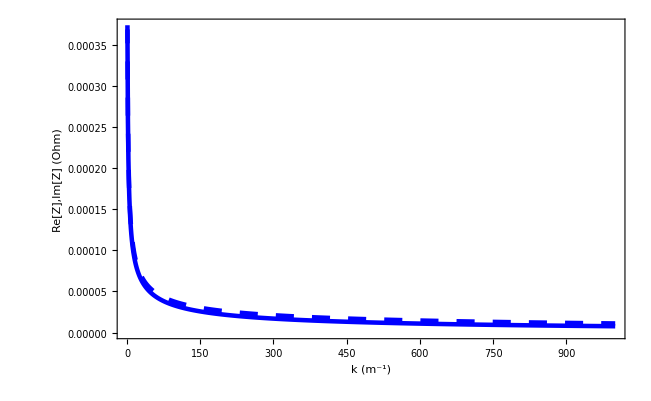

```mathematica
p=0.5 10^-3;(*period*)
t=0.25 10^-3 ;(*Longitudinal gap*)
a=500 10^-6 ;(*Distance from the plate*)
Zr=Table[{k,Re[Z l[k,a, t, p]]},{k,1,1000,1.}];Zi=Table[{k,Im[Z l[k,a, t, p]]},{k,1,1000,1.}];
p1=ListLinePlot[{Zr,Zi},Frame->True,PlotRange->{Full,Full},FrameLabel->{"k (m^-1)","Re[Z],Im[Z] (Ohm)"},PlotStyle->{{Thickness[0.005],Blue},{Thickness[0.005],Blue,Dashing[{0.02,0.02}]}},LabelStyle->{Large},BaseStyle->{FontFamily->"Helvetica"}];
Show[p1]
```

```mathematica
σz=7.5*10^-6; (* Nominal Gaussian bunch length *)
dz=5.*10^-7; (* Step size for numerical integration *)
kmax=1000; (* Maximum wavenumber for CSR impedance calculation *)
c0=3 10^8
Zr1=Interpolation[Zr];
Zi1=Interpolation[Zi];
```

300000000

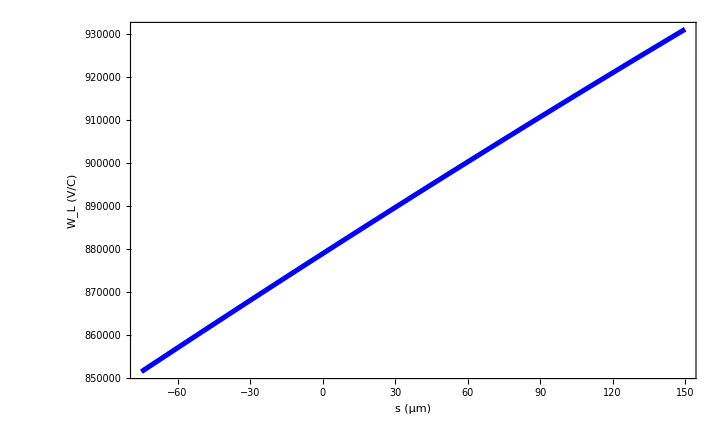

```mathematica
WsRWanalytic1=Table[{i*dz 10^6,Wake1tmp[i*dz, Zr1, Zi1, σz]},{i,-Round[10 σz/dz],Round[20σz/dz]}];
p2=ListLinePlot[{WsRWanalytic1},Frame->True,PlotRange->{Full,Full},FrameLabel->{"s (μm)","W_L (V/C)"},PlotStyle->{{Thickness[0.005],Blue},{Thickness[0.005],Blue}},LabelStyle->{Large},BaseStyle->{FontFamily->"Helvetica"}];
Show[p2]
```

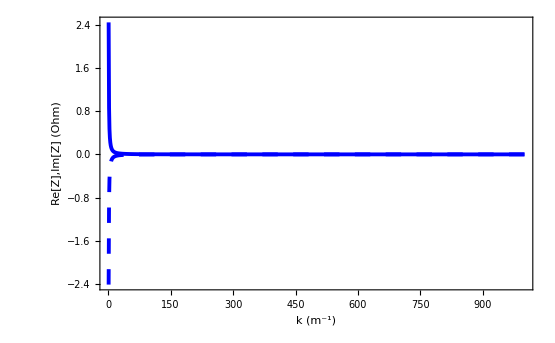

```mathematica
y=0;
Zrf=Table[{k,Re[Zlflat[k, y,a, t, p]]},{k,1,1000,1.}];Zif=Table[{k,Im[Zlflat[k, y,a, t, p]]},{k,1,1000,1.}];
p1=ListLinePlot[{Zrf,Zif},Frame->True,PlotRange->{Full,Full},FrameLabel->{"k (m^-1)","Re[Z],Im[Z] (Ohm)"},PlotStyle->{{Thickness[0.005],Blue},{Thickness[0.005],Blue,Dashing[{0.02,0.02}]}},LabelStyle->{Large},BaseStyle->{FontFamily->"Helvetica"}];
Show[p1]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {4.09622}. NIntegrate obtained 4.78872 and 0.000796242 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {4.09622}. NIntegrate obtained 4.78867 and 0.00079624 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {4.09622}. NIntegrate obtained 4.78861 and 0.000796239 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

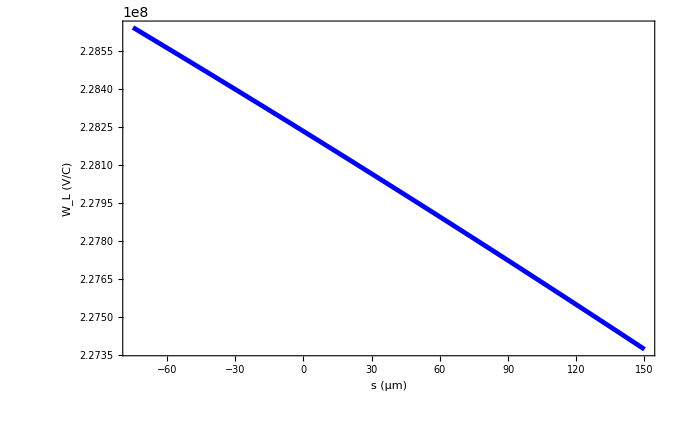

```mathematica
Zrf1=Interpolation[Zrf];
Zif1=Interpolation[Zif];

WsRWanalytic=Table[{i*dz 10^6,Wake1tmp[i*dz, Zrf1, Zif1, σz]},{i,-Round[10 σz/dz],Round[20σz/dz]}];
p2=ListLinePlot[{WsRWanalytic},Frame->True,PlotRange->{Full,Full},FrameLabel->{"s (μm)","W_L (V/C)"},PlotStyle->{{Thickness[0.005],Blue},{Thickness[0.005],Blue}},LabelStyle->{Large},BaseStyle->{FontFamily->"Helvetica"}];
Show[p2]
```

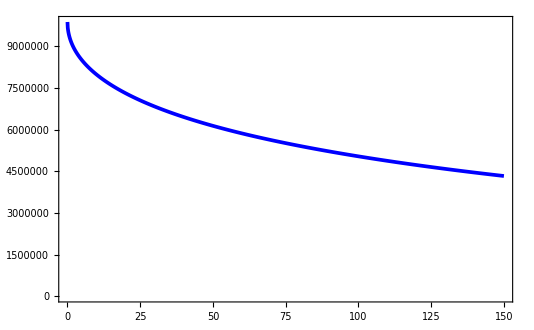

```mathematica
Wf=Table[{s 10^6,wakez[s, 0, a, t, p]},{s,0,15 10^-5,0.1 10^-6}];
p2=ListLinePlot[{Wf},Frame->True,PlotRange->{Full,Full},PlotStyle->{{Thickness[0.005],Blue},{Thickness[0.005],Blue}},LabelStyle->{Large},BaseStyle->{FontFamily->"Helvetica"}];
Show[p2]
```